# Ejemplo 2 Manivela - Corredera

## Funciones

```mathematica
(*Matrices de Rotación*)
Rx[γ_]:=({{1, 0, 0}, {0, Cos[γ], -Sin[γ]}, {0, Sin[γ], Cos[γ]}});
Ry[β_]:=({{Cos[β], 0, Sin[β]}, {0, 1, 0}, {-Sin[β], 0, Cos[β]}});
Rz[α_]:=({{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0, 0, 1}});

MatrixForm[Rx[A]]
MatrixForm[Ry[A]]
MatrixForm[Rz[A]]
```

(1 | 0 | 0
0 | Cos[A] | -Sin[A]
0 | Sin[A] | Cos[A])

(Cos[A] | 0 | Sin[A]
0 | 1 | 0
-Sin[A] | 0 | Cos[A])

(Cos[A] | -Sin[A] | 0
Sin[A] | Cos[A] | 0
0 | 0 | 1)

## Datos

```mathematica
x21=0.15;(*m*)
y43=0.15;
x87=0.6;
y98=0.04;
x1110=0.3;
y1211=0.04;
x1413=0.25;
z1615=0.9;
z1918=0.25;

β10=330*Degree;
β1716=180*Degree;
β1817=90*Degree;
```

## Ecuaciones Cinemáticas

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];
(*-----------------------------Posicion-----------------------------*)
I3x3 = IdentityMatrix[3];

in={1,0,0};
jn={0,1,0};
kn={0,0,1};
I0=in;
J0=jn;
K0=kn;
(*_______________Matrices de rotación____________*)
(*Junta rotacional*)
C01=Ry[β10];(*Rotación sobre y/j*)
C02=Ry[β10];(*Paralelo al anterior*)
C03=Ry[β10].Rx[θ32];(*Rotación sobre x/i*)
C04=Ry[β10].Rx[θ32];(*Paralelo al anterior*)
(*Junta Esférica*)
C05=Ry[β10].Rx[θ32].Rx[θ54];(*Rotación sobre x/i*)
C06=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65];(*Rotación sobre y/j*)
C07=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76];(*Rotación sobre z/k*)
(*Junta rotacional 2*)
C08=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76];(*Paralelo al anterior*)
C09=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76];(*Paralelo al anterior*)
C010=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109];(*Rotación sobre y/j*)
(*Junta Rotacional 3*)
C011=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109];(*Paralelo al anterior*)
C012=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109];(*Paralelo al anterior*)
C013=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109].Ry[θ1312];(*Rotación sobre y/j*)
(*Junta Rotacional 4*)
C014=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109].Ry[θ1312];(*Paralelo al anterior*)
C015=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109].Ry[θ1312].Rx[θ1514];(*Rotación sobre x/i*)
C016=Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109].Ry[θ1312].Rx[θ1514];(*Paralelo al anterior*)
C017=C016.Rz[β1716];(*Rotación sobre z/k*)
C018=C017.Ry[β1817];(*Rotación sobre y/j*)
C019=C018;(*Paralelo al anterior*)

(*__________Dirección de los vectores__________*)
(*Posición*)
I1=C01.in;
J3=C03.jn;
I7=C07.in;
J8=C08.jn;
I10=C010.in;
J11=C011.jn;
I13=C013.in;
K15=C015.kn;
K18=C018.kn;
(*Velocidad*)
I2=C02.in;
I4=C04.in;
J5=C05.jn;
K6=C06.kn;
J9=C09.jn;
J12=C012.jn;(*Rotación y*)
I14=C014.in;(*Rotación x*)

(*__________Velocidades angulares__________*)
ω32=dθ32*I2;(*Rotación x*)
ω54=dθ54*I4;(*Rotación x*)
ω65=dθ65*J5;(*Rotación y*)
ω76=dθ76*K6;(*Rotación z*)
ω109=dθ109*J9;(*Rotación y*)
ω1312=dθ1312*J12;(*Rotación y*)
ω1514=dθ1514*I14;(*Rotación x*)

ω3=ω32;
ω7=ω32+ω54+ω65+ω76;
ω8=ω7;(*????*)
ω10=ω32+ω54+ω65+ω76+ω109;
(*ω11=ω32+ω54+ω65+ω76+ω109+ω1312;*)
ω11=ω32+ω54+ω65+ω76+ω109;

(*__________Aceleraciones angulares__________*)

α32=ddθ32*I2;
α54=ddθ54*I4+ω32×ω54;
α65=ddθ65*J5+(ω32+ω54)×ω65;
α76=ddθ76*K6+(ω32+ω54+ω65)×ω76;
α109=ddθ109*J9+(ω32+ω54+ω65+ω76)×ω109;
α1312=ddθ1312*J12+(ω32+ω54+ω65+ω76+ω109)×ω1312;
α1514=ddθ1514*I14+(ω32+ω54+ω65+ω76+ω109+ω1312)×ω1514;

α3=α32;
α7=α32+α54+α65+α76;
α8=α7;(*????*)
α10=α32+α54+α65+α76+α109;
α11=α32+α54+α65+α76+α109+α1312;

(*__________Definición de vectores__________*)
(*Posición*)
P21=x21*I1;
P43=y43*J3;
P87=x87*I7;
P98=y98*J8;
P1110=x1110*I10;
P1211=-y1211*J11;
P1413=x1413*I13;
P1615=z1615*K15;
P1918=z1918*K18;
(*Velocidad*)
V21={0,0,0};(*No cambia de dirección ni magnitud*)
V43=ω3×P43;(*Cambia solo de dirección*)
V87=ω7×P87;(*Cambia solo de dirección*)
V98=ω8×P98;(*Cambia solo de dirección*)
V1110=ω10×P1110;(*Cambia solo de dirección*)
V1211=ω11×P1211;(*Cambia solo de dirección*)
V1413={0,0,0};(*No cambia de dirección ni magnitud*)
V1615={0,0,0};(*No cambia de dirección ni magnitud*)
V1918={0,0,0};(*No cambia de dirección ni magnitud*)
(*Aceleración*)
A21={0,0,0};(*No cambia de dirección ni magnitud*)
A43=α3×P43+ω3×(ω3×P43);(*Cambia solo de dirección*)
A87=α7×P87+ω7×(ω7×P87);(*Cambia solo de dirección*)
A98=α8×P98+ω8×(ω8×P98);(*Cambia solo de dirección*)
A1110=α10×P1110+ω10×(ω10×P1110);(*Cambia solo de dirección*)
A1211=α11×P1211+ω11×(ω11×P1211);(*Cambia solo de dirección*)
A1413={0,0,0};(*No cambia de dirección ni magnitud*)
A1615={0,0,0};(*No cambia de dirección ni magnitud*)
A1918={0,0,0};(*No cambia de dirección ni magnitud*)

(*-----------------------------Ecuaciones de Posición-----------------------------*)
Pos1 = P21+P43+P87+P98+P1110+P1211+P1413+P1615+P1918;
Pos2 =Ry[β10].Rx[θ32].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ109].Ry[θ1312].Rx[θ1514].Rz[β1716].Ry[β1817]-I3x3;
(*-----------------------------Ecuaciones de Velocidad-----------------------------*)

(*FO = Funcion objetivo*)
FO = ∑_(i=1)^3 Pos1[[i]]^2+∑_(j=1)^3 ∑_(k=1)^3 Pos2[[j,k]]^2;

Vel1 = V21+V43+V87+V98+V1110+V1211+V1413+V1615+V1918;
Vel2=ω32+ω54+ω65+ω76+ω109+ω1312+ω1514;

Acel1 = A21+A43+A87+A98+A1110+A1211+A1413+A1615+A1918;
Acel2=α32+α54+α65+α76+α109+α1312+α1514;


MatrixForm[Pos1]
MatrixForm[Pos2]
```

(0.129904-0.075 Sin[θ32]+0.6 (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76])+0.3 (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))+0.25 (Cos[θ1312] (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))-Sin[θ1312] (Cos[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Sin[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76])))+0.25 (-Cos[θ1312] (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))+Sin[θ1312] (Cos[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Sin[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76])))+0.9 (-Sin[θ1514] (Cos[θ76] (-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54])-(1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65]) Sin[θ76])+Cos[θ1514] (Sin[θ1312] (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Sin[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))))
0.+0.15 Cos[θ32]+0.6 (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76])+0.3 (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))+0.25 (Cos[θ1312] (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))-Sin[θ1312] (Cos[θ109] Cos[θ65] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Sin[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76])))+0.25 (-Cos[θ1312] (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))+Sin[θ1312] (Cos[θ109] Cos[θ65] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Sin[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76])))+0.9 (-Sin[θ1514] (Cos[θ76] (Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54])+(-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65] Sin[θ76])+Cos[θ1514] (Sin[θ1312] (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] Cos[θ65] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Sin[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))))
0.075+0.129904 Sin[θ32]+0.6 (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76])+0.3 (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))+0.25 (Cos[θ1312] (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))-Sin[θ1312] (Cos[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Sin[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76])))+0.25 (-Cos[θ1312] (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))+Sin[θ1312] (Cos[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Sin[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76])))+0.9 (-Sin[θ1514] (Cos[θ76] (1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54])-(Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65]) Sin[θ76])+Cos[θ1514] (Sin[θ1312] (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Sin[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76])))))

(-1+Sin[θ1514] (Cos[θ76] (-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54])-(1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65]) Sin[θ76])-Cos[θ1514] (Sin[θ1312] (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Sin[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))) | -Cos[θ1514] (Cos[θ76] (-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54])-(1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65]) Sin[θ76])-Sin[θ1514] (Sin[θ1312] (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Sin[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))) | -Cos[θ1312] (-Sin[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Cos[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))+Sin[θ1312] (Cos[θ109] (Cos[θ65] (-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54])+1/2 √3 Sin[θ65])+Sin[θ109] (Cos[θ76] (1/2 √3 Cos[θ65]-(-1/2 Cos[θ32] Cos[θ54]+1/2 Sin[θ32] Sin[θ54]) Sin[θ65])+(-1/2 Cos[θ54] Sin[θ32]-1/2 Cos[θ32] Sin[θ54]) Sin[θ76]))
Sin[θ1514] (Cos[θ76] (Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54])+(-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65] Sin[θ76])-Cos[θ1514] (Sin[θ1312] (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] Cos[θ65] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Sin[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))) | -1-Cos[θ1514] (Cos[θ76] (Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54])+(-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65] Sin[θ76])-Sin[θ1514] (Sin[θ1312] (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] Cos[θ65] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Sin[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))) | -Cos[θ1312] (-Cos[θ65] Sin[θ109] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Cos[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))+Sin[θ1312] (Cos[θ109] Cos[θ65] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54])+Sin[θ109] (-Cos[θ76] (-Cos[θ54] Sin[θ32]-Cos[θ32] Sin[θ54]) Sin[θ65]+(Cos[θ32] Cos[θ54]-Sin[θ32] Sin[θ54]) Sin[θ76]))
Sin[θ1514] (Cos[θ76] (1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54])-(Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65]) Sin[θ76])-Cos[θ1514] (Sin[θ1312] (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Sin[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))) | -Cos[θ1514] (Cos[θ76] (1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54])-(Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65]) Sin[θ76])-Sin[θ1514] (Sin[θ1312] (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))+Cos[θ1312] (Cos[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Sin[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))) | -1-Cos[θ1312] (-Sin[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Cos[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76]))+Sin[θ1312] (Cos[θ109] (Cos[θ65] (1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54])+Sin[θ65]/2)+Sin[θ109] (Cos[θ76] (Cos[θ65]/2-(1/2 √3 Cos[θ32] Cos[θ54]-1/2 √3 Sin[θ32] Sin[θ54]) Sin[θ65])+(1/2 √3 Cos[θ54] Sin[θ32]+1/2 √3 Cos[θ32] Sin[θ54]) Sin[θ76])))

## Solución de la Posición

### Solución inicial

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];
θ32=0*Degree;
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
PosInicial=FindMinimum[FO,
{
{θ54,Random[]},
{θ65,Random[]},
{θ76,Random[]},
{θ109,61*Degree},
{θ1312,42*Degree},
{θ1514,168*Degree}
}, MaxIterations ->25]
(*FindMinimum entrega un valor residual*)

{θ32,θ54,θ65,θ76,θ109,θ1312,θ1514}/Degree/.PosInicial[[2]]
```

{1.6876×10^-28,{θ54→-0.0485152,θ65→0.281497,θ76→-0.173222,θ109→1.07529,θ1312→0.741662,θ1514→2.94922}}

{0,-2.77972,16.1286,-9.92491,61.6093,42.4941,168.978}

### Dibujo:Solución inicial

```mathematica
(*Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];*)
θ32=0*Degree;
Pos1 = P21+P43+P87+P98+P1110+P1211+P1413+P1615+P1918;
P0={0,0,0};
P1=P21;
P2=P21+P43;
P3=P21+P43+P87;
P4=P21+P43+P87+P98;
P5=P21+P43+P87+P98+P1110;
P6=P21+P43+P87+P98+P1110+P1211;
P7=P21+P43+P87+P98+P1110+P1211+P1413;
P8=P21+P43+P87+P98+P1110+P1211+P1413+P1615;
P9=P21+P43+P87+P98+P1110+P1211+P1413+P1615+P1918;

P0e =Sphere[{0,0,0},0.015]/.PosInicial[[2]]
P1e =Sphere[P1,0.015]/.PosInicial[[2]];
P2e =Sphere[P2,0.015]/.PosInicial[[2]];
P3e =Sphere[P3,0.015]/.PosInicial[[2]];
P4e =Sphere[P4,0.015]/.PosInicial[[2]];
P5e =Sphere[P5,0.015]/.PosInicial[[2]];
P6e =Sphere[P6,0.015]/.PosInicial[[2]];
P7e =Sphere[P7,0.015]/.PosInicial[[2]];
P8e =Sphere[P8,0.015]/.PosInicial[[2]];
P9e =Sphere[P9,0.015]/.PosInicial[[2]]

Origen = Graphics3D[{RGBColor[0,1,0],P0e}];
Puntos=Graphics3D[{RGBColor[1,0,0],P1e,P2e,P3e,P4e,P5e,P6e,P7e,P8e,P9e}];

Show[Puntos,Origen,
ImageSize->500,
ViewPoint->{2.7872,1.2068,1.4899},
ViewVertical->{0,1,0}]

(*(*Manivela*)
Manivela=Tube[{P0,P1,P2},0.006]/.PosInicial[[2]];
ManEsf=Sphere[P2,0.01]/.PosInicial[[2]];(*Junta esférica*)
(*Barra1*)
Ba1Esf=Sphere[P2,0.015]/.PosInicial[[2]];(*Junta esférica*)
Barra1 = Tube[{P2,P3},0.007]/.PosInicial[[2]];(*Cuerpo Barra 1*)
CilBar1 = Cylinder[{P3,P4},0.009]/.PosInicial[[2]];
(*Barra2*)
Barra2 = Tube[{P4,P5},0.006]/.PosInicial[[2]];(*Cuerpo Barra 2*)
CilBar2 = Cylinder[{P5,P6},0.009]/.PosInicial[[2]];
(*Barra3*)
Barra3 = Tube[{P6,P7},0.006]/.PosInicial[[2]];(*Cuerpo Barra 3*)
(*Base*)
Pmin1={-0.12,0.15,-0.25};
Pmax1={1,-0.15,-0.27};
Cubo1=Cuboid[Pmin1,Pmax1];
(*Cara 1 Prisma 1*)
a1={-0.039,-0.1,-0.2};
b1={0.071,-0.1,-0.2};
c1={-0.039,-0.1,0.1};

(*Cara 2 Prisma 1*)
a2={-0.039,0.1,-0.2};
b2={0.071,0.1,-0.2};
c2={-0.039,0.1,0.1};
Prisma1=Prism[{a1,b1,c1,a2,b2,c2}];
Cuerpo1=Graphics3D[{GrayLevel[0.913725],Cubo1,Prisma1}];(*Base*)
Cuerpo2=Graphics3D[{RGBColor[0,1,0],Manivela,ManEsf}];(*Manivela*)
Cuerpo3=Graphics3D[{RGBColor[1,0,0],Ba1Esf,Barra1,CilBar1}];(*Barra1*)
Cuerpo4=Graphics3D[{RGBColor[0,0,1],Barra2,CilBar2}];(*Barra2*)
Cuerpo5=Graphics3D[{RGBColor[0,1,1],Barra3}];(*Barra3*)
Show[Cuerpo1,Cuerpo2,Cuerpo3,Cuerpo4,Cuerpo5,
ImageSize->500,
ViewPoint->{2.7872,1.2068,1.4899},
ViewVertical->{0,1,0}]*)
```

Sphere[{0,0,0},0.015]

Sphere[{-9.4369×10^-15,-2.0664×10^-15,4.42404×10^-15},0.015]

-Graphics3D-

### Solución Total

```mathematica
(*Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];
θ32=0*Degree*)

θ54i=θ54/.PosInicial[[2]];
θ65i=θ65/.PosInicial[[2]];
θ76i=θ76/.PosInicial[[2]];
θ109i=θ109/.PosInicial[[2]];
θ1312i=θ1312/.PosInicial[[2]];
θ1514i=θ1514/.PosInicial[[2]];

For[i=0, i<=360, i+=1,
θ32=i*Degree;
SolPos[i]=FindMinimum[FO,
{
{θ54,θ54i},
{θ65,θ65i},
{θ76,θ76i},
{θ109,θ109i},
{θ1312,θ1312i},
{θ1514,θ1514i}
}, MaxIterations ->15];
θ54i=θ54/.SolPos[i][[2]];
θ65i=θ65/.SolPos[i][[2]];
θ76i=θ76/.SolPos[i][[2]];
θ109i=θ109/.SolPos[i][[2]];
θ1312i=θ1312/.SolPos[i][[2]];
θ1514i=θ1514/.SolPos[i][[2]];
];
SolPos[0]
```

{1.6876×10^-28,{θ54→-0.0485152,θ65→0.281497,θ76→-0.173222,θ109→1.07529,θ1312→0.741662,θ1514→2.94922}}

## Gráficas de la Posición

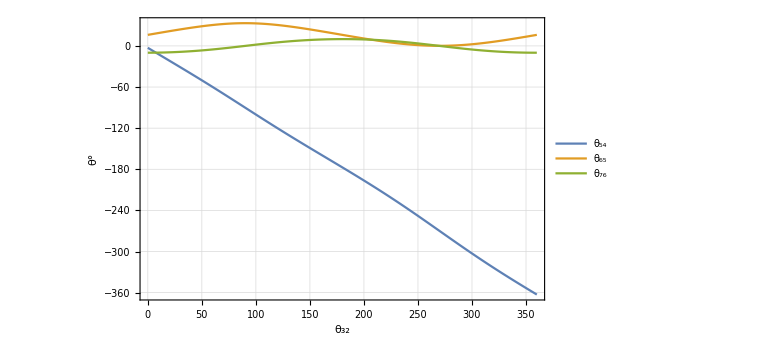

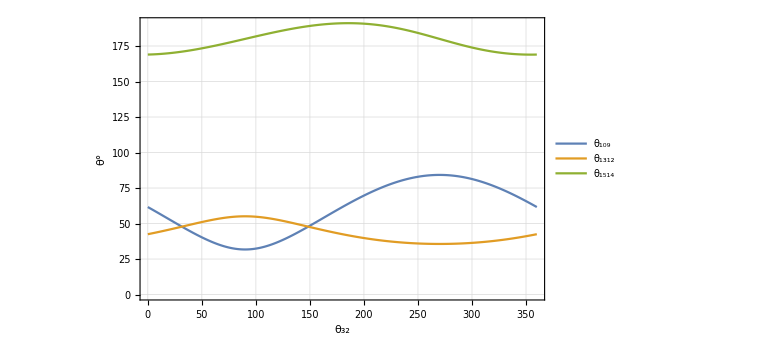

```mathematica
PTable1 = Table[{i,θ54/Degree}/.SolPos[i][[2]],{i,0,360,1}];(*Tabla 1 posición*)
PTable2 = Table[{i,θ65/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable3 = Table[{i,θ76/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable4 = Table[{i,θ109/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable5 = Table[{i,θ1312/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable6 = Table[{i,θ1514/Degree}/.SolPos[i][[2]],{i,0,360,1}];
TablaAngulos = {PTable1,PTable2,PTable3};
TablaAngulos2 = {PTable4,PTable5,PTable6};
ListLinePlot[TablaAngulos,PlotLegends->{"θ_54", "θ_65","θ_76"},
Frame->True,FrameLabel->{"θ_32", "θ°"},GridLines->Automatic, ImageSize->Large
]
ListLinePlot[TablaAngulos2,PlotLegends->{"θ_109","θ_1312","θ_1514"},
Frame->True,FrameLabel->{"θ_32", "θ°"},GridLines->Automatic, ImageSize->Large
]
```

## Solución de la Velocidad

```mathematica
Vel1/.PosInicial[[2]]//MatrixForm//Chop
Vel2/.PosInicial[[2]]//MatrixForm//Chop
```

(-0.217124 dθ109+0.075 dθ54-0.0812116 dθ65+0.141985 dθ76
0.0422915 dθ109+0.45 dθ32+0.45 dθ54-0.0305246 dθ65+0.728945 dθ76
-0.202654 dθ109-0.129904 dθ54-0.772827 dθ65)

(0.191188 dθ109+0.191188 dθ1312+(√3 dθ32)/2+(√3 dθ54)/2+0.0242481 dθ65-0.239178 dθ76
0.981553 dθ109+0.981553 dθ1312+0.998823 dθ65+0.0465874 dθ76
-1. dθ1514+dθ32/2+dθ54/2-0.0419989 dθ65+0.969857 dθ76)

### Solución inicial

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];
θ32=0*Degree;
dθ32=2π;(*1 vuelta en 1 segundo*)
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
VelInicial=Solve[{
Vel1[[1]]==0,
Vel1[[2]]==0,
Vel1[[3]]==0,

Vel2[[1]]==0,
Vel2[[2]]==0,
Vel2[[3]]==0}/.PosInicial[[2]],
{ dθ54, dθ65, dθ76,dθ109,dθ1312,dθ1514}]//Flatten
```

{dθ54→-5.94371,dθ65→1.7014,dθ76→0.0170692,dθ109→-2.67833,dθ1312→0.946186,dθ1514→0.114834}

### Solución Total

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];

dθ32=2π/1;(*1 vuelta en 1 segundo*)

For[i=0, i<=360, i+=1,
θ32=i*Degree;
(*θ21=90*Degree;*)
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
SolVel[i]=Solve[{
Vel1[[1]]==0,
Vel1[[2]]==0,
Vel1[[3]]==0,

Vel2[[1]]==0,
Vel2[[2]]==0,
Vel2[[3]]==0}/.SolPos[i][[2]],
{dθ54, dθ65, dθ76, dθ109,dθ1312,dθ1514}]//Flatten;

];(*Cierra el FOR*)
SolVel[0]
```

{dθ54→-5.94371,dθ65→1.7014,dθ76→0.0170692,dθ109→-2.67833,dθ1312→0.946186,dθ1514→0.114834}

## Gráficas de la Velocidad.

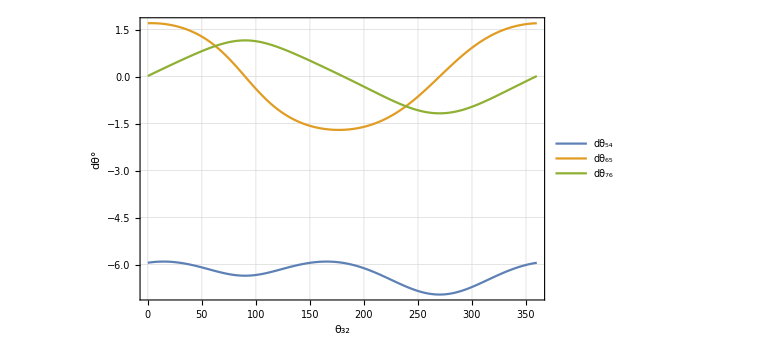

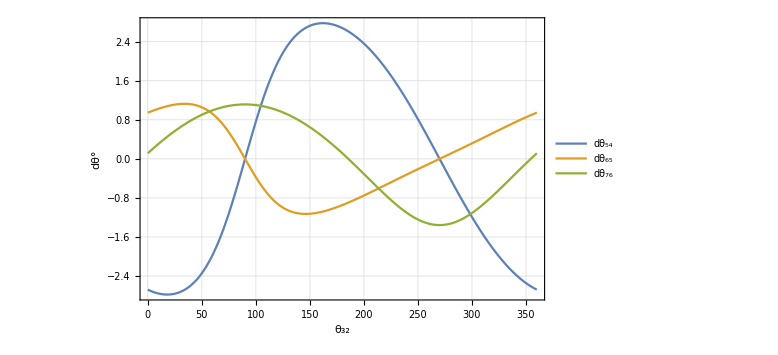

```mathematica
(*Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];*)

VTable1 = Table[{i,dθ54}/.SolVel[i],{i,0,360,1}];(*Tabla 1 posición*)
VTable2 = Table[{i,dθ65}/.SolVel[i],{i,0,360,1}];
VTable3 = Table[{i,dθ76}/.SolVel[i],{i,0,360,1}];
VTable4 = Table[{i,dθ109}/.SolVel[i],{i,0,360,1}];
VTable5 = Table[{i,dθ1312}/.SolVel[i],{i,0,360,1}];
VTable6 = Table[{i,dθ1514}/.SolVel[i],{i,0,360,1}];
VTablaAngulos1 = {VTable1, VTable2, VTable3};
VTablaAngulos2 = {VTable4, VTable5,VTable6};

ListLinePlot[VTablaAngulos1,PlotLegends->{"dθ_54", "dθ_65", "dθ_76", "dθ_109", "dθ_1312","dθ_1514"},
Frame->True,FrameLabel->{"θ_32", "dθ°"},GridLines->Automatic, ImageSize->Large
]
ListLinePlot[VTablaAngulos2,PlotLegends->{"dθ_54", "dθ_65", "dθ_76", "dθ_109", "dθ_1312","dθ_1514"},
Frame->True,FrameLabel->{"θ_32", "dθ°"},GridLines->Automatic, ImageSize->Large
]
```

## Solución de la Aceleración.

```mathematica
Acel1/.PosInicial[[2]]/.VelInicial//MatrixForm//Chop
Acel2/.PosInicial[[2]]/.VelInicial//MatrixForm//Chop
```

(-1.48823-0.0390165 ddθ32+0.0350601 ddθ54+0.118334 ddθ65-0.216152 (-0.186383+0.982515 ddθ109+0.999217 ddθ65+0.0374941 ddθ76)+0.0387324 (0.604321+ddθ32/2+ddθ54/2-0.0342536 ddθ65+0.979512 ddθ76)+0.0393006 (0.604321+ddθ32/2+ddθ54/2-0.0342536 ddθ65+0.979512 ddθ76)+0.0732141 ddθ76
-4.9864+0.164332 ddθ32+0.187797 ddθ54-0.0224238 ddθ65+0.216152 (0.747546+0.186182 ddθ109+(√3 ddθ32)/2+(√3 ddθ54)/2+0.0197763 ddθ65-0.197863 ddθ76)+0.204397 (0.604321+ddθ32/2+ddθ54/2-0.0342536 ddθ65+0.979512 ddθ76)-0.0074473 (0.604321+ddθ32/2+ddθ54/2-0.0342536 ddθ65+0.979512 ddθ76)+0.596804 ddθ76
-0.886292-0.208035 ddθ109+0.0340353 ddθ32-0.0942692 ddθ54-0.790811 ddθ65-0.0393006 (0.45597+0.186182 ddθ109+0.186182 ddθ1312+(√3 ddθ32)/2+(√3 ddθ54)/2+0.0197763 ddθ65-0.197863 ddθ76)+0.0074473 (-0.13113+0.982515 ddθ109+0.982515 ddθ1312+0.999217 ddθ65+0.0374941 ddθ76)-0.00805535 ddθ76)

(0.45597+0.186182 ddθ109+0.186182 ddθ1312+(√3 ddθ32)/2+(√3 ddθ54)/2+0.0197763 ddθ65-0.197863 ddθ76
-0.13113+0.982515 ddθ109+0.982515 ddθ1312+0.999217 ddθ65+0.0374941 ddθ76
0.604321-1. ddθ1514+ddθ32/2+ddθ54/2-0.0342536 ddθ65+0.979512 ddθ76)

### Solución inicial

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];
θ32=0*Degree;
dθ32=2π/1;(*1 vuelta en 1 segundo*)
ddθ32=0;
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
AcelInicial=Solve[{
Acel1[[1]]==0,
Acel1[[2]]==0,
Acel1[[3]]==0,

Acel2[[1]]==0,
Acel2[[2]]==0,
Acel2[[3]]==0}/.PosInicial[[2]]/.VelInicial,
{ddθ54, ddθ65, ddθ76, ddθ109,ddθ1312,ddθ1514}]//Flatten
```

{ddθ54→0.707773,ddθ65→-0.72672,ddθ76→5.93752,ddθ109→-2.04843,ddθ1312→2.69438,ddθ1514→6.79898}

### Solución Total

```mathematica
Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];

dθ32=2π/1;(*1 vuelta en 1 segundo*)
ddθ32=0;

For[i=0, i<=360, i+=1,
θ32=i*Degree;
(*θ21=90*Degree;*)
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
SolAcel[i]=Solve[{
Acel1[[1]]==0,
Acel1[[2]]==0,
Acel1[[3]]==0,

Acel2[[1]]==0,
Acel2[[2]]==0,
Acel2[[3]]==0}/.SolPos[i][[2]]/.SolVel[i],
{ddθ54, ddθ65, ddθ76, ddθ109,ddθ1312,ddθ1514}]//Flatten;

];(*Cierra el FOR*)
SolAcel[0]
```

{ddθ54→0.707773,ddθ65→-0.72672,ddθ76→5.93752,ddθ109→-2.04843,ddθ1312→2.69438,ddθ1514→6.79898}

## Gráficas de la Aceleración.

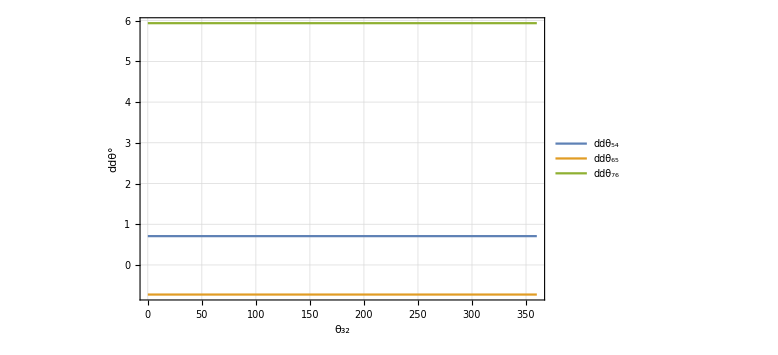

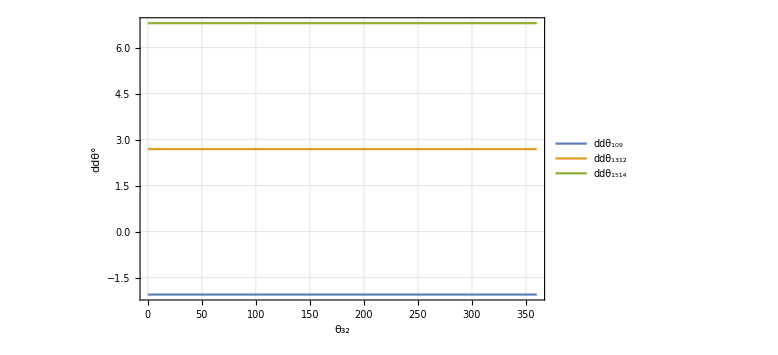

```mathematica
(*Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];*)

ATable1 = Table[{i,ddθ54}/.SolAcel[i],{i,0,360,1}];(*Tabla 1 posición*)
ATable2 = Table[{i,ddθ65}/.SolAcel[i],{i,0,360,1}];
ATable3 = Table[{i,ddθ76}/.SolAcel[i],{i,0,360,1}];
ATable4 = Table[{i,ddθ109}/.SolAcel[i],{i,0,360,1}];
ATable5 = Table[{i,ddθ1312}/.SolAcel[i],{i,0,360,1}];
ATable6 = Table[{i,ddθ1514}/.SolAcel[i],{i,0,360,1}];
ATablaAngulos1 = {ATable1, ATable2, ATable3};
ATablaAngulos2 ={ATable4, ATable5, ATable6};
ListLinePlot[ATablaAngulos1,PlotLegends->{"ddθ_54", "ddθ_65", "ddθ_76"},
Frame->True,FrameLabel->{"θ_32", "ddθ°"},GridLines->Automatic, ImageSize->Large
]
ListLinePlot[ATablaAngulos2,PlotLegends->{ "ddθ_109", "ddθ_1312","ddθ_1514"},
Frame->True,FrameLabel->{"θ_32", "ddθ°"},GridLines->Automatic, ImageSize->Large
]
```

## Animación con ANIMATE.

```mathematica
(*Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];*)

Animate[
θ32=i*Degree;

P0={0,0,0};
P1=P21;
P2=P21+P43;
P3=P21+P43+P87;
P4=P21+P43+P87+P98;
P5=P21+P43+P87+P98+P1110;
P6=P21+P43+P87+P98+P1110+P1211;
P7=P21+P43+P87+P98+P1110+P1211+P1413;

(*Manivela*)
Manivela=Tube[{P0,P1,P2},0.009]/.SolPos[i][[2]];
Cilindro1=Cylinder[{P0,P0+0.1*P1},0.015]/.SolPos[i][[2]];
(*Barra1*)
Ba1Esf=Sphere[P2,0.017]/.SolPos[i][[2]];(*Junta esférica*)
Barra1 = Tube[{P2,P3,P3+(0.5*P98)},0.009]/.SolPos[i][[2]];(*Cuerpo Barra 1*)
(*Barra2*)
Barra2 = Tube[{P4-(0.5*P98),P4,P5,P5+(0.5*P1211)},0.009]/.SolPos[i][[2]];(*Cuerpo Barra 2*)
(*Barra3*)
Barra3 = Tube[{P6-(0.5*P1211),P6,P7},0.009]/.SolPos[i][[2]];(*Cuerpo Barra 3*)
Cilindro2=Cylinder[{P6+(0.9*P1413),P7}, 0.015]/.SolPos[i][[2]];
(*Base*)
Pmin1={-0.12,0.15,-0.25};
Pmax1={1,-0.15,-0.27};
Cubo1=Cuboid[Pmin1,Pmax1];
(*Cara 1 Prisma 1*)
a1={-0.039,-0.1,-0.25};
b1={0.071,-0.1,-0.25};
c1={-0.039,-0.1,0.1};

(*Cara 2 Prisma 1*)
a2={-0.039,0.1,-0.25};
b2={0.071,0.1,-0.25};
c2={-0.039,0.1,0.1};
Prisma1=Prism[{a1,b1,c1,a2,b2,c2}];
Cuerpo1=Graphics3D[{RGBColor[255/255,218/255,185/255],EdgeForm[None],Opacity[1],Cubo1,Prisma1,Lighting -> "Neutral"}];(*Base*)
Cuerpo2=Graphics3D[{RGBColor[34/255,139/255,34/255],EdgeForm[None],JoinForm["Miter"],JoinForm["Miter"],Manivela,Cilindro1}];(*Manivela*)
Cuerpo3=Graphics3D[{RGBColor[255/255,69/255,0],JoinForm["Miter"],CapForm["Butt"],Ba1Esf,Barra1}];(*Barra1*)
Cuerpo4=Graphics3D[{RGBColor[25/255,25/255,112/255],JoinForm["Miter"],CapForm["Butt"],Barra2}];(*Barra2*)
Cuerpo5=Graphics3D[{RGBColor[255/255,215/255,0/255],EdgeForm[None],JoinForm["Miter"],CapForm["Butt"],Barra3,Cilindro2}];(*Barra3*)


Show[Cuerpo1,Cuerpo2,Cuerpo3,Cuerpo4,Cuerpo5,
Axes->True,
AxesLabel->{"X","Y","Z"},
ImageSize->500,
ViewPoint->{2.7872,1.2068,1.4899},
ViewVertical->{0,0,1},
PlotRange->{{-0.15,1.05},{-0.17,0.17},{-0.27,0.27}}
],{i,0,360,1},AnimationRunning-> False,ControlPlacement->Top]
```

## Animación con FOR par GIF.

```mathematica
(*Clear[θ32,θ54,θ65,θ76,θ109,θ1312,θ1514];
Clear[dθ32,dθ54,dθ65,dθ76,dθ109,dθ1312,dθ1514];
Clear[ddθ32,ddθ54,ddθ65,ddθ76,ddθ109,ddθ1312,ddθ1514];*)
For[i=0,i<=360,i+=1,
θ32=i*Degree;

P0={0,0,0};
P1=P21;
P2=P21+P43;
P3=P21+P43+P87;
P4=P21+P43+P87+P98;
P5=P21+P43+P87+P98+P1110;
P6=P21+P43+P87+P98+P1110+P1211;
P7=P21+P43+P87+P98+P1110+P1211+P1413;

(*Manivela*)
Manivela=Tube[{P0,P1,P2},0.009]/.SolPos[i][[2]];
Cilindro1=Cylinder[{P0,P0+0.1*P1},0.015]/.SolPos[i][[2]];
(*Barra1*)
Ba1Esf=Sphere[P2,0.017]/.SolPos[i][[2]];(*Junta esférica*)
Barra1 = Tube[{P2,P3,P3+(0.5*P98)},0.009]/.SolPos[i][[2]];(*Cuerpo Barra 1*)
(*Barra2*)
Barra2 = Tube[{P4-(0.5*P98),P4,P5,P5+(0.5*P1211)},0.009]/.SolPos[i][[2]];(*Cuerpo Barra 2*)
(*Barra3*)
Barra3 = Tube[{P6-(0.5*P1211),P6,P7},0.009]/.SolPos[i][[2]];(*Cuerpo Barra 3*)
Cilindro2=Cylinder[{P6+(0.9*P1413),P7}, 0.015]/.SolPos[i][[2]];
(*Base*)
Pmin1={-0.12,0.15,-0.25};
Pmax1={1,-0.15,-0.27};
Cubo1=Cuboid[Pmin1,Pmax1];
(*Cara 1 Prisma 1*)
a1={-0.039,-0.1,-0.25};
b1={0.071,-0.1,-0.25};
c1={-0.039,-0.1,0.1};

(*Cara 2 Prisma 1*)
a2={-0.039,0.1,-0.25};
b2={0.071,0.1,-0.25};
c2={-0.039,0.1,0.1};
Prisma1=Prism[{a1,b1,c1,a2,b2,c2}];
Cuerpo1=Graphics3D[{RGBColor[255/255,218/255,185/255],EdgeForm[None],Opacity[1],Cubo1,Prisma1,Lighting -> "Neutral"}];(*Base*)
Cuerpo2=Graphics3D[{RGBColor[34/255,139/255,34/255],EdgeForm[None],JoinForm["Miter"],JoinForm["Miter"],Manivela,Cilindro1}];(*Manivela*)
Cuerpo3=Graphics3D[{RGBColor[255/255,69/255,0],JoinForm["Miter"],CapForm["Butt"],Ba1Esf,Barra1}];(*Barra1*)
Cuerpo4=Graphics3D[{RGBColor[25/255,25/255,112/255],JoinForm["Miter"],CapForm["Butt"],Barra2}];(*Barra2*)
Cuerpo5=Graphics3D[{RGBColor[255/255,215/255,0/255],EdgeForm[None],JoinForm["Miter"],CapForm["Butt"],Barra3,Cilindro2}];(*Barra3*)


Animacion[i]=Show[Cuerpo1,Cuerpo2,Cuerpo3,Cuerpo4,Cuerpo5,
Axes->True,
AxesLabel->{"X","Y","Z"},
ImageSize->500,
ViewPoint->{2.7872,1.2068,1.4899},
ViewVertical->{0,0,1},
PlotRange->{{-0.15,1.05},{-0.17,0.17},{-0.27,0.27}}
]];
Mecanismos





(*Show[Cuerpo1,Cuerpo2,Cuerpo3,Cuerpo4,Cuerpo5,
Axes->True,
AxesLabel->{"X","Y","Z"},
ImageSize->500,
ViewPoint->{2.7872,1.2068,1.4899},
ViewVertical->{0,0,1},
PlotRange->{{-0.15,1.05},{-0.17,0.17},{-0.27,0.27}}
],{i,0,360,1},AnimationRunning-> False,ControlPlacement->Top]*)
```

Mecanismos

```mathematica
TablaFiguras = Table[Animacion[i], {i, 0, 360, 10}];
Export["/home/yeshua/Documentos/sem_10/DinamicaMaquinaria/animacion_gif/mecanismo_examen.gif", TablaFiguras]
```

/home/yeshua/Documentos/sem_10/DinamicaMaquinaria/animacion_gif/mecanismo_examen.gif